## Cria a matriz

```mathematica
matriz=({{e, t, 0, 0, 0}, {t, e, t, 0, 0}, {0, t, e, t, 0}, {0, 0, t, e, t}, {0, 0, 0, t, e}})
```

{{e,1,0,0,0},{1,e,1,0,0},{0,1,e,1,0},{0,0,1,e,1},{0,0,0,1,e}}

```mathematica
{valores, vetores}=Eigensystem[matriz] /.e->0 /.t->1
```

{{-1,0,1,-√3,√3},{{-1,1,0,-1,1},{1,0,-1,0,1},{-1,-1,0,1,1},{1,-√3,2,-√3,1},{1,√3,2,√3,1}}}

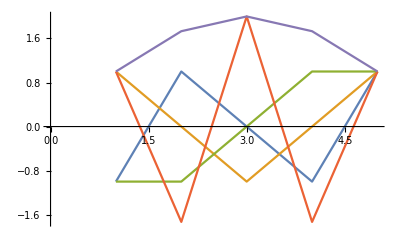

```mathematica
ListPlot[vetores, Joined -> True]
```

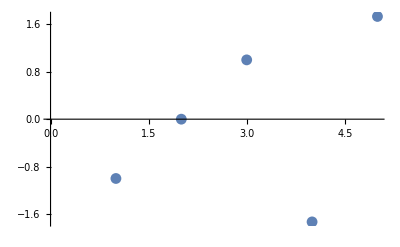

```mathematica
ListPlot[valores]
```

## Criar o hamiltoniano com Sparce Array

```mathematica
s=SparseArray[
{
{i_,i_}->2,
{i_,j_}/;Abs[i-j] == 1->1
},
  {10,10}
]
```

SparseArray[<28>, {10, 10}]

```mathematica
Normal[s]//MatrixForm
```

(2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2)

```mathematica
{valoress,vetoress}=Eigensystem[Normal[s]]
```

{{1/43 (6+9 1),8,1/43 1},1}
 |  |  |  |

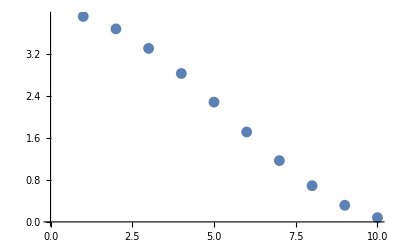

```mathematica
ListPlot[valoress]
```

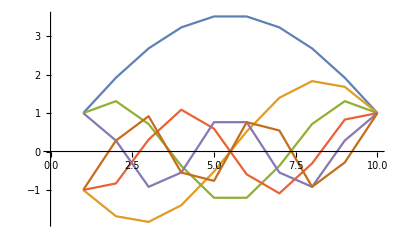

```mathematica
ListPlot[vetoress[[1;;6]], Joined -> True]
```

## Hamiltoniano de um anel

```mathematica
anel=SparseArray[
{
{i_,i_}->2,
{i_,j_}/;(i-j) == 1->1-0.00000001 I,
{i_,j_}/; (j-i)==1 ->1+0.00000001 I,
{1,5}-> 1-0.00000001I,
{5,1}->1 + 0.00000001I
},
  {5,5}
]
```

SparseArray[<15>, {5, 5}]

No anel todas as ondas planas deveriam ter a mesma amplitude de probabilidade, no entanto os arredondamentos do programa tornam as as ondas harmónicas. 
Para corrigir introduzimos uma pequena componente imaginaria para causar degenerescência.

SparseArray[<30>, {10, 10}]

```mathematica
Normal[anel]//MatrixForm
```

(2 | 1.+1.×10^-8 ⅈ | 0 | 0 | 1.-1.×10^-8 ⅈ
1.-1.×10^-8 ⅈ | 2 | 1.+1.×10^-8 ⅈ | 0 | 0
0 | 1.-1.×10^-8 ⅈ | 2 | 1.+1.×10^-8 ⅈ | 0
0 | 0 | 1.-1.×10^-8 ⅈ | 2 | 1.+1.×10^-8 ⅈ
1.+1.×10^-8 ⅈ | 0 | 0 | 1.-1.×10^-8 ⅈ | 2)

```mathematica
{valanel,vetanel}=Eigensystem[Normal[anel]]
```

{{4.,2.61803,2.61803,0.381966,0.381966},{{-0.447214+1.62638×10^-23 ⅈ,-0.447214+2.20856×10^-23 ⅈ,-0.447214-1.24485×10^-23 ⅈ,-0.447214-1.31843×10^-23 ⅈ,-0.447214+0. ⅈ},{0.138197-0.425325 ⅈ,-0.361803-0.262866 ⅈ,-0.361803+0.262866 ⅈ,0.138197+0.425325 ⅈ,0.447214+0. ⅈ},{-0.138197-0.425325 ⅈ,0.361803-0.262866 ⅈ,0.361803+0.262866 ⅈ,-0.138197+0.425325 ⅈ,-0.447214+0. ⅈ},{-0.361803-0.262866 ⅈ,0.138197+0.425325 ⅈ,0.138197-0.425325 ⅈ,-0.361803+0.262866 ⅈ,0.447214+0. ⅈ},{-0.361803+0.262866 ⅈ,0.138197-0.425325 ⅈ,0.138197+0.425325 ⅈ,-0.361803-0.262866 ⅈ,0.447214+0. ⅈ}}}

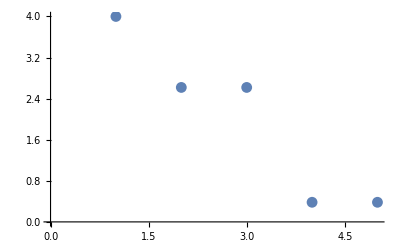

```mathematica
ListPlot[valanel]
```

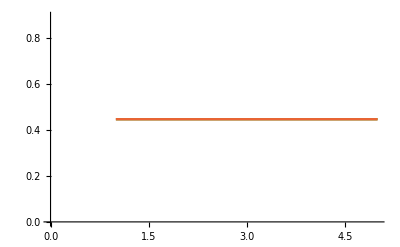

```mathematica
ListPlot[Abs[vetanel[[1;;4]]],Joined -> True]
```

## Matriz de anel com fases

```mathematica
anelf=SparseArray[
{
{i_,i_} -> 0,
{i_,j_} /; (i-j)==1 -> p Exp[- I phi/5],
{i_,j_} /; (j-i)==1 -> p Exp[I phi/5],
{1,5}-> p Exp[-I phi/5],
{5,1}-> p Exp[I phi/5]
},
{5,5}]
```

SparseArray[<10>, {5, 5}]

```mathematica
Normal[anelf]//MatrixForm
```

(0 | ⅇ^((ⅈ phi)/5) p | 0 | 0 | ⅇ^(-(ⅈ phi)/5) p
ⅇ^(-(ⅈ phi)/5) p | 0 | ⅇ^((ⅈ phi)/5) p | 0 | 0
0 | ⅇ^(-(ⅈ phi)/5) p | 0 | ⅇ^((ⅈ phi)/5) p | 0
0 | 0 | ⅇ^(-(ⅈ phi)/5) p | 0 | ⅇ^((ⅈ phi)/5) p
ⅇ^((ⅈ phi)/5) p | 0 | 0 | ⅇ^(-(ⅈ phi)/5) p | 0)

```mathematica
Manipulate[
{anelfval, anelfvet}= Eigensystem[Normal[anelf]/.p->1 /.phi -> phivalue];
ListPlot[anelfvet,Joined->True],
{{phivalue,0},0,3,0.001}
]
```

ListPlot::lpn: {{0.447214  + 0.\ ⅈ, 0.447214  + 0.\ ⅈ, 0.447214  + 0.\ ⅈ, 0.447214  + 0.\ ⅈ, 0.447214  + 0.\ ⅈ}, {0.199649  + 0.\ ⅈ, 0.191221  + 0.\ ⅈ, -0.50905 + 0.\ ⅈ, 0.63244  + 0.\ ⅈ, -0.514259 + 0.\ ⅈ}, {0.632456  + 0.\ ⅈ, -0.511667 + 0.\ ⅈ, « 20 »  + « 1 », « 20 »  + 0.\ ⅈ, -0.511667 + 0.\ ⅈ}, {0.0218911  + 0.\ ⅈ, 0.607905  + 0.\ ⅈ, 0.353815  + 0.\ ⅈ, -0.389236 + 0.\ ⅈ, -0.594376 + 0.\ ⅈ}, {0.632456  + 0.\ ⅈ, 0.19544  + 0.\ ⅈ, -0.511667 + 0.\ ⅈ, -0.511667 + 0.\ ⅈ, 0.19544  + 0.\ ⅈ}} is not a list of numbers or pairs of numbers.

ListPlot::lpn: {{-0.447214 + 1.7637×10^-17\ ⅈ, -0.447214 + 2.24375×10^-17\ ⅈ, -0.447214 - 1.86835×10^-17\ ⅈ, -0.447214 - 1.76593×10^-17\ ⅈ, -0.447214 + 0.\ ⅈ}, {-0.361803 + 0.262866\ ⅈ, 0.138197  - 0.425325\ ⅈ, 0.138197  + 0.425325\ ⅈ, -0.361803 - 0.262866\ ⅈ, 0.447214  + 0.\ ⅈ}, {« 20 »  + « 19 »\ ⅈ, « 4 »}, {« 1 »}, {-0.138197 - 0.425325\ ⅈ, 0.361803  - 0.262866\ ⅈ, 0.361803  + 0.262866\ ⅈ, -0.138197 + 0.425325\ ⅈ, -0.447214 + 0.\ ⅈ}} is not a list of numbers or pairs of numbers.

ListPlot::lpn: {{0.447214 + 0.\\ ⅈ, 0.447214 + 0.\\ ⅈ, 0.447214 + 0.\\ ⅈ, 0.447214 + 0.\\ ⅈ, 0.447214 + 0.\\ ⅈ}, {0.199649 + 0.\\ ⅈ, 0.191221 + 0.\\ ⅈ, -0.50905 + 0.\\ ⅈ, 0.63244 + 0.\\ ⅈ, -0.514259 + 0.\\ ⅈ}, {0.632456 + 0.\\ ⅈ, -0.511667 + 0.\\ ⅈ, «20» + «1», «20» + 0.\\ ⅈ, -0.511667 + 0.\\ ⅈ}, {0.0218911 + 0.\\ ⅈ, 0.607905 + 0.\\ ⅈ, 0.353815 + 0.\\ ⅈ, -0.389236 + 0.\\ ⅈ, -0.594376 + 0.\\ ⅈ}, {0.632456 + 0.\\ ⅈ, 0.19544 + 0.\\ ⅈ, -0.511667 + 0.\\ ⅈ, -0.511667 + 0.\\ ⅈ, 0.19544 + 0.\\ ⅈ}} is not a list of numbers or pairs of numbers. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/ListPlot",
ButtonNote->"ListPlot::lpn"]

ListPlot::lpn: {{-0.447214 + 1.7637×10^-17\ ⅈ, -0.447214 + 2.24375×10^-17\ ⅈ, -0.447214 - 1.86835×10^-17\ ⅈ, -0.447214 - 1.76593×10^-17\ ⅈ, -0.447214 + 0.\ ⅈ}, {-0.361803 + 0.262866\ ⅈ, 0.138197  - 0.425325\ ⅈ, 0.138197  + 0.425325\ ⅈ, -0.361803 - 0.262866\ ⅈ, 0.447214  + 0.\ ⅈ}, {« 20 »  + « 19 »\ ⅈ, « 4 »}, {« 1 »}, {-0.138197 - 0.425325\ ⅈ, 0.361803  - 0.262866\ ⅈ, 0.361803  + 0.262866\ ⅈ, -0.138197 + 0.425325\ ⅈ, -0.447214 + 0.\ ⅈ}} is not a list of numbers or pairs of numbers.